# Learning XOR

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## Get data

```mathematica
numBooleanVariables=10; (* 2^numBooleanVariables possible inputs *)
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=Min[2000,2^numBooleanVariables];
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->bf@@x]&,Range[maxExamples]];
```

```mathematica
Take[examples,3]
```

{{1.,1.,0.,0.,1.,1.,0.,0.,0.,0.}→False,{0.,0.,1.,0.,1.,1.,1.,1.,0.,1.}→False,{1.,0.,0.,0.,1.,1.,0.,1.,1.,0.}→True}

```mathematica
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
targetEncoder=NetEncoder[{"Class",{True,False},"IndicatorVector"}];
```

## Create net

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=22*numClasses},
HardNeuralChain[{
HardNeuralNOT[inputSize,classificationLayerSize],
HardNeuralMajority[classificationLayerSize,inputSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=64*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralNAND[classificationLayerSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
trainableSoftNet=NetGraph[<|"NeuralLogicNet"->softNet,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"},"Target"->targetEncoder];
```

```mathematica
NetFlatten[trainableSoftNet]
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableSoftNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,{},
"Output"->NetDecoder[targetEncoder]]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]
]};
```

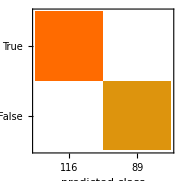
{Classifier Measurements
Classifier method | Net
Number of test examples | 205
Accuracy | (100.00000000000000022) %
Accuracy baseline | (56.63.5) %
Geometric mean of probabilities | 0.986 ± 0.0017
Mean cross entropy | 0.014 ± 0.0017
Single evaluation time | 2.13 ms/example
Batch evaluation speed | 2.34 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 205
Accuracy | (100.00000000000000022) %
Accuracy baseline | (56.63.5) %
Geometric mean of probabilities | 0.986 ± 0.0017
Mean cross entropy | 0.014 ± 0.0017
Single evaluation time | 2.2 ms/example
Batch evaluation speed | 9.8 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[targetEncoder],First[#]&,Last[#]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

1.

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[First[#]],"Target"->Last[#]}]&/@testData;
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

1.

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

0.0537109 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize]
```

{{Majority[b1,b10,b2,b6,b7,!b3,!b4,!b5,!b8,!b9],Majority[b1,b10,b3,b4,b5,b7,b9,!b2,!b6,!b8],Majority[b2,b3,b4,b6,b7,!b1,!b10,!b5,!b8,!b9],Majority[b1,b4,b6,b7,b9,!b10,!b2,!b3,!b5,!b8],Majority[b2,b5,b6,b7,b9,!b1,!b10,!b3,!b4,!b8],Majority[b1,b4,b6,b7,b8,!b10,!b2,!b3,!b5,!b9],Majority[b1,b10,b4,b5,b8,!b2,!b3,!b6,!b7,!b9],Majority[b10,b3,b5,b8,b9,!b1,!b2,!b4,!b6,!b7],Majority[b1,b3,b6,!b10,!b2,!b4,!b5,!b7,!b8,!b9],Majority[b2,b3,b4,b5,b8,!b1,!b10,!b6,!b7,!b9],Majority[b1,b3,b4,b5,b6,b8,b9,!b10,!b2,!b7],Majority[b1,b6,b7,b8,b9,!b10,!b2,!b3,!b4,!b5],Majority[b4,b5,b6,b7,b9,!b1,!b10,!b2,!b3,!b8],Majority[b3,b4,b5,b6,b8,!b1,!b10,!b2,!b7,!b9],Majority[b1,b10,b4,b6,b7,!b2,!b3,!b5,!b8,!b9],Majority[b1,b10,b2,b3,b5,b6,b7,!b4,!b8,!b9],Majority[b1,b10,b8,!b2,!b3,!b4,!b5,!b6,!b7,!b9],Majority[b2,b3,b5,b7,b9,!b1,!b10,!b4,!b6,!b8],Majority[b10,b2,b3,b6,b7,b8,b9,!b1,!b4,!b5],Majority[b1,b10,b2,b3,b6,b7,b9,!b4,!b5,!b8],Majority[b10,b2,b3,b5,b9,!b1,!b4,!b6,!b7,!b8],Majority[b1,b2,b5,b7,b8,!b10,!b3,!b4,!b6,!b9]},{Majority[b1,b10,b2,b5,b7,b9,!b3,!b4,!b6,!b8],Majority[b1,b10,b2,b3,b5,b6,!b4,!b7,!b8,!b9],Majority[b3,b7,!b1,!b10,!b2,!b4,!b5,!b6,!b8,!b9],Majority[b2,b4,b6,b8,!b1,!b10,!b3,!b5,!b7,!b9],Majority[b1,b10,b4,b7,b8,b9,!b2,!b3,!b5,!b6],Majority[b1,b10,b3,b4,b5,b7,!b2,!b6,!b8,!b9],Majority[b1,b10,b2,b6,b7,b8,!b3,!b4,!b5,!b9],Majority[b1,b2,b6,b9,!b10,!b3,!b4,!b5,!b7,!b8],Majority[b3,b4,b5,b6,!b1,!b10,!b2,!b7,!b8,!b9],Majority[b1,b4,b5,b6,b7,b9,!b10,!b2,!b3,!b8],Majority[b10,b2,b3,b4,b6,b7,b8,b9,!b1,!b5],Majority[b10,b3,b6,b7,b8,b9,!b1,!b2,!b4,!b5],Majority[b1,b3,b6,b9,!b10,!b2,!b4,!b5,!b7,!b8],Majority[b1,b10,b2,b3,b5,b7,b8,b9,!b4,!b6],Majority[b10,b2,b4,b5,b7,b8,!b1,!b3,!b6,!b9],Majority[b1,b2,b3,b4,b5,b6,b8,b9,!b10,!b7],Majority[b1,b3,b4,b5,b6,b7,!b10,!b2,!b8,!b9],Majority[b1,b8,!b10,!b2,!b3,!b4,!b5,!b6,!b7,!b9],Majority[b1,b4,b5,b6,b7,b9,!b10,!b2,!b3,!b8],Majority[b10,b3,b5,b6,!b1,!b2,!b4,!b7,!b8,!b9],Majority[b2,b5,b6,b9,!b1,!b10,!b3,!b4,!b7,!b8],Majority[b1,b10,b3,b5,b7,b8,!b2,!b4,!b6,!b9]}}

## Train standard net

```mathematica
classifier=Classify[trainData->"Target",Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

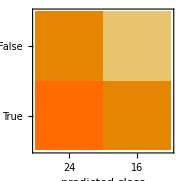
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 40
Accuracy | (55.8.) %
Accuracy baseline | (60.8.) %
Geometric mean of probabilities | 0.464 ± 0.038
Mean cross entropy | 0.768 ± 0.081
Single evaluation time | 4.81 ms/example
Batch evaluation speed | 518. examples/s
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Target"]
```

```mathematica
(First@classifier)["Model"]["Network"]
```

NetChain[<>]

```mathematica
Information[classifier,"FunctionMemory"]
```

290. kB

```mathematica
HNM[inputs_]:={Sort[inputs][[Floor[(Length[inputs]+1)/2]]],First[HardNeuralMajority[1,4]][{inputs}],Majority@@Harden[inputs]}
```

```mathematica
HNM[inputs_]:=With[{hnm=HardNeuralMajority[1,Length[inputs]]},{hnm[[1]][{inputs}],First[hnm[[2]][{{Harden[inputs]},{}}]]}]
```

```mathematica
Manipulate[HNM[{b1,b2,b3,b4}],{b1,0,1},{b2,0,1},{b3,0,1},{b4,0,1}]
```